```mathematica
- I hbar Delta/2/Pi Integrate[ξ Exp[-I ξ (a-b)Delta],{ξ,-Pi/Delta,Pi/Delta}]
```

$Aborted

```mathematica
Delta/2/Pi Integrate[ξ ^2 Exp[-I ξ (a-b)Delta],{ξ,-Pi/Delta,Pi/Delta}]/.{a->1,b->2}//FullSimplify
```

-2/Delta^2

```mathematica
"\\langle" //ToExpression
```

$Failed

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/Guide-for-ugrs-in-linjun-group/fig
```

```mathematica
a=Import["/Users/Apple/Documents/GitHub/SincDVR/output/harmonic3.out","Table"];
```

```mathematica
Export["/Users/Apple/Documents/GitHub/Guide-for-ugrs-in-linjun-group/fig/DVRtest.eps",ListLinePlot[Map[Function[q,{#[[2]],#[[5]]}&/@Partition[Last/@Select[q,Length[#]==3&],5]],{a,b}],PlotRange->{{0,50},Automatic},Frame->True,Axes->False,FrameLabel->{"t (a.u.)","<x> (a.u.)"},PlotLegends->{"dt = 0.01","dt = 0.1"}]]
```

/Users/Apple/Documents/GitHub/Guide-for-ugrs-in-linjun-group/fig/DVRtest.eps

```mathematica
b=Import["/Users/Apple/Documents/GitHub/SincDVR/harmonicbad.out","Table"];
```

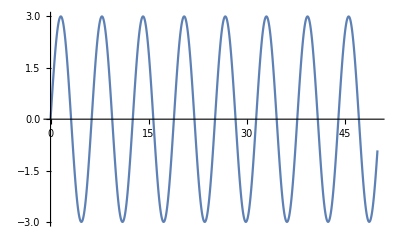

```mathematica
ListLinePlot[{#[[2]],#[[4]]}&/@Partition[Last/@Select[a,Length[#]==3&],5]]
```

```mathematica
ListLinePlot[{#[[2]],#[[5]]}&/@Partition[Last/@Select[a,Length[#]==1&],201]]
```

```mathematica
Manipulate[ListLinePlot[(First/@Partition[Partition[Last/@Select[a,Length[#]==1&],201],2])[[i]],PlotRange->All],{i,1,1000}]
```

```mathematica
Table[i+j-2,{i,3},{j,3}]//MatrixForm
```

(0 | 1 | 2
1 | 2 | 3
2 | 3 | 4)

```mathematica
Eigensystem[Table[i+j-2,{i,3},{j,3}]]//N
```

{{6.87298,-0.872983,0.},{{0.392281,0.69614,1.},{-1.82085,-0.410426,1.},{1.,-2.,1.}}}

```mathematica
FourierTransform[1/x,x,k]
```

ⅈ √(π/2) Sign[k]

```mathematica
Integrate[Exp[- I k x]/x,{x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(-ⅈ k x)/x does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-ⅈ k x)/x ⅆx

```mathematica
Residue[Exp[- I k x]/x,{x,0}]
```

1

```mathematica
Delta/2/Pi Integrate[Exp[-I ξ (i-j)Delta],{ξ,-Pi/Delta,Pi/Delta}]
```

(Delta Sin[(i-j) π])/((Delta i-Delta j) π)

```mathematica
-I hbar Δx/2/Pi Integrate[I ξ Exp[-I ξ (i-j)Δx],{ξ,-Pi/Δx,Pi/Δx}]
```

-(ⅈ hbar ((-i+j) π Cos[(i-j) π]+Sin[(i-j) π]))/((i-j)^2 π Δx)

```mathematica
Solve[{B1 R + P/R^2==A1/R^2,B1-(2 P)/R^3==(-2 A1)/R^3 ϵr},{A1,B1}]
```

{{A1→(3 P)/(1+2 ϵr),B1→-(2 P (-1+ϵr))/(R^3 (1+2 ϵr))}}

```mathematica
5*365*60*60*24*9.8
```

1.54526×10^9

```mathematica
1/Sqrt[1-u^2/c^2] 1/Sqrt[1-v^2/c^2](1+u v/c^2)(m0 (c^2 - u v))/Sqrt[1-v^2/c^2]//FullSimplify
```

(m0 (c^4-u^2 v^2))/(√(1-u^2/c^2) (c^2-v^2))

```mathematica
1/Sqrt[1-u^2/c^2] 1/Sqrt[1-v^2/c^2](1+u v/c^2)(m0 (c^2 - u v))/Sqrt[1-v^2/c^2]/((m0 c^2)/Sqrt[1-((u+v)/(1+((u v)/c^2)))^2/c^2])//FullSimplify
```

(√(1-u^2/c^2) (c^2-u v))/(√(((c-u) (c+u) (c-v) (c+v))/((c^2+u v)^2)) (c^2+u v))

```mathematica
(m0 c^2)/Sqrt[1-((u+v)/(1+((u v)/c^2)))^2/c^2]
```

(c^2 m0)/(√(1-(u+v)^2/(c^2 (1+(u v)/c^2)^2)))